Here we present an example of our running calculation. We run the wilson coefficients for 3 operators in the SMEFT from 10 TeV to M_Top. At M_Top and below we use the WET with the top quark integrated out. The 3 wilson coefficients in the SMEFT contribute to the matching of a single wilson coefficient in the WET at M_Top. We then run this single wilson coefficient down to 1 GeV.

```mathematica
Quit[];
```

```mathematica
1+1//Timing
```

{8.×10^-6,2}

```mathematica
<<"/Users/noahsteinberg/Library/Mathematica/Applications/DsixTools/DsixTools.m"
```

DsixTools 1.1.3

by Alejandro Celis, Javier Fuentes-Martin, Avelino Vicente and Javier Virto

Reference: arXiv:1704.04504

Website: https://dsixtools.github.io/

This program is free software: you can redistribute it and/or modify it under the terms of the GNU General Public License as published by the Free Software Foundation, either version 3 of the License, or any later version.

See ?DsixTools`* for a list of routines and variables.

#### Set our low scale to M_Top and our high scale to 10 TeV

## Options

```mathematica
LOWSCALE=80.385;
HIGHSCALE=10^16;
mh = 125.7;
CPV=0;
ReadRGEs=1;
RGEsMethod=1;
ExportRGEs=0;
UseRGEsSM=1;
exportSMEFTrunner=0;
exportEWmatcher=0;
exportWETrunner=0;
inputWCsType=1;
Init[g]=e/Sin[θW];
Init[gp]=e/Cos[θW];
Init[gs]=Sqrt[4Pi (0.120502)];
Init[λ]=mh^2/v^2;
Init[m2]=mh^2/2;
Init[GU[1,1]]=1.23231*10^-5;
Init[GU[1,2]]=-1.64215*10^-3;
Init[GU[1,3]]=5.90635*10^-3;
Init[GU[2,1]]=2.84527*10^-6;
Init[GU[2,2]]=7.10724*10^-3;
Init[GU[2,3]]=-4.18547*10^-2;
Init[GU[3,1]]=4.65426*10^-8;
Init[GU[3,2]]=3.08758*10^-4;
Init[GU[3,3]]=0.994858;
Init[GD[1,1]]=2.70195*10^-5;
Init[GD[1,2]]=0;
Init[GD[1,3]]=0;
Init[GD[2,1]]=0;
Init[GD[2,2]]=5.51888*10^-4;
Init[GD[2,3]]=0;
Init[GD[3,1]]=0;
Init[GD[3,2]]=0;
Init[GD[3,3]]=2.403012*10^-2;
Init[GE[1,1]]=2.93766*10^-6;
Init[GE[1,2]]=0;
Init[GE[1,3]]=0;
Init[GE[2,1]]=0;
Init[GE[2,2]]=6.07422*10^-4;
Init[GE[2,3]]=0;
Init[GE[3,1]]=0;
Init[GE[3,2]]=0;
Init[GE[3,3]]=1.02157*10^-2;
Init[θ]=0;
Init[θp]=0;
Init[θs]=0;
```

## Set Wilson coefficients at High Scale (10 TeV in this example)

```mathematica
φ,φ□
```

```mathematica
FindParameterSMEFT[φ□]
```

{41}

```mathematica
SetDirectory[NotebookDirectory[]];
WriteAndReadInputFiles["Options_program4.dat","WCsInput_program4.dat","SMInput_program4.dat"];
```

Input : SMEFT Wilson coefficients

```mathematica
LoadModule["SMEFTrunner"]
LoadBetaFunctions;
RunRGEsSMEFT;
```

LoadModule::Already: Warning : SMEFTrunner module already loaded

Loading SMEFT β functions

Running

Running finished!

Run Wilson coefficients from 10TeV to M_Top

```mathematica
param1 = FindParameterSMEFT[λ];
```

Plot Wilson coefficients from 10 TeV to M_Top

```mathematica
tLOW=Log10[LOWSCALE]
tHIGH=Log10[HIGHSCALE]
```

1.90518

16

```mathematica
tHIGH
```

4

```mathematica
Exp[tLOW]
```

9.37994

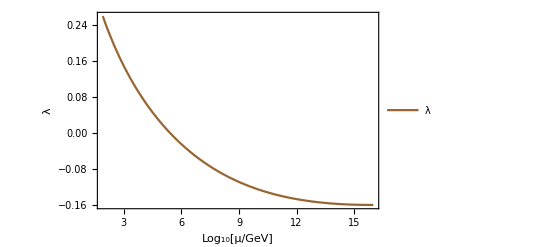

```mathematica
plotWC7=Plot[outSMEFTrunner[[param1]],{t,tLOW,tHIGH},Frame->True,Axes->False,PlotRange->{{10^tLOW,10^tHIGH},Automatic}, PlotLegends->{"λ"}, PlotStyle->{Brown}, PlotRange->Automatic];
Show[plotWC7,PlotRange->Automatic, FrameLabel->{"Log_10[μ/GeV]","λ"},LabelStyle->{Black,18}]
```

Now we match the SMEFT Wilson coefficients to the WET Wilson coefficients

```mathematica
Subscript[V, 11]= .97427;
Subscript[V, 21] = .22520;
Subscript[V, 31] = .00867;
Subscript[V, 12] = .22534;
Subscript[V, 22] = .97344;
Subscript[V, 32] = .0404;
Subscript[V, 13] = .00351;
Subscript[V, 23] = .0412;
Subscript[V, 33] = .999146;

CLRudsnutau= -(Subscript[V, 12](outSMEFTrunner[[param1]]/.t->tLOW )+ Subscript[V, 22](outSMEFTrunner[[param2]]/.t->tLOW) + Subscript[V, 32](outSMEFTrunner[[param3]]/.t->tLOW));
CLRudsnutau
```

{-0.0000729831}

Now we run the above matched Wilson coefficient, “CLRudsnutau” down to 1GeV using RunDec. We consider only QCD contributions and run at the 2 loop level.

```mathematica
<<"/Users/noahsteinberg/Desktop/BNV_Mathematica_Programs/RunDec.m"
```

RunDec: a Mathematica package for running and decoupling of the

strong coupling and quark masses

by K.G. Chetyrkin, J.H. K\"uhn and M. Steinhauser (January 2000)

by F. Herren and M. Steinhauser (April 2016, v2.1)

```mathematica
ALRQCDtop[mt_, MZ_, mb_, mc_, p0_, as5MZ_]:= Module[{as5mt, as5mb, as4mb, as4mc, as3mc,as3p0},
as5mt = AlphasExact[as5MZ, MZ, mt, 5, 4];
as5mb = AlphasExact[as5MZ,MZ,mb,5,4];
as4mb = DecAsDownMS[as5mb, mb, mb, 4, 4];
as4mc = AlphasExact[as4mb,mb, mc, 4, 4];
as3mc = DecAsDownMS[as4mc, mc, mc, 3, 4];
as3p0 = AlphasExact[as3mc, mc, p0, 3, 4];
Return[(as3p0/as3mc)^(6/27)(as4mc/as4mb)^(6/25)(as5mb/as5mt)^(6/23)((as3p0 + (9π)/16)/(as3mc + (9π)/16))^(-29/144)((as4mc + (50π)/77)/(as4mb + (50π)/77))^(-173/825)((as5mb + (23π)/29)/(as5mt + (23π)/29))^(-430/2001)];]
```

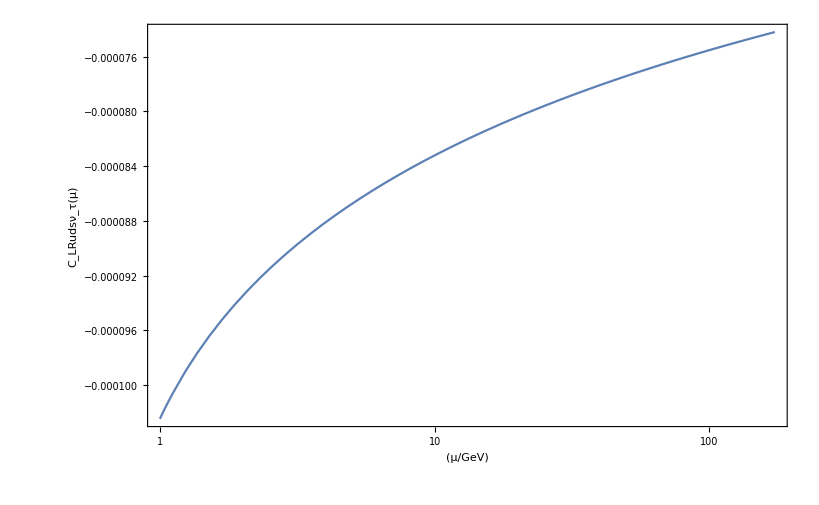

```mathematica
CudsnutauLR = LogLinearPlot[CLRudsnutau*ALRQCDtop[173.21, 91.1876, 4.18, 1.28,  p, 0.1185], {p, 1.0, 173.21}, Frame->True, FrameLabel->{"(μ/GeV)", "C_LRudsν_τ(μ)"}, LabelStyle->{Black,18}]
```

Above plot is the Wilson coefficient CLR_udsnutau(μ). CLR_udsnutau(1 GeV) is the Wilson coefficient we will use when calculating the proton decay rate. This completes the running of the Wilson Coefficients from below Msusy to 1GeV

```mathematica
CLRudsnutau*ALRQCDtop[173.21, 91.1876, 4.18,1.28, 1, 0.1185]
```

{-0.000102473}